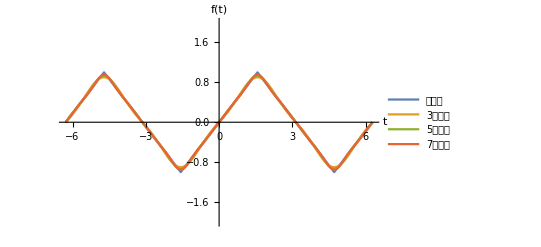

```mathematica
Clear["Global`*"]

f[t_]:=2/Pi ArcSin[Sin[t]]

S[n_,t_]:=8/Pi^2 Sum[(-1)^k Sin[(2 k+1) t]/(2 k+1)^2,{k,0,(n-1)/2}](*阶数为2k+1，令n=2k+1，所以k=（n-1）/2，求出上限*)

Plot[{f[t],S[3,t],S[5,t],S[7,t]},{t,-2 Pi,2 Pi},PlotRange->{-2,2},PlotLegends->{"原函数","3阶展开","5阶展开","7阶展开"},AxesLabel->{"t","f(t)"}]
```